```mathematica
At=Import["C:\\Output_1881695243.txt","Table"];
```

```mathematica
h=0.001;

M=MatrixForm[At]; 
Kx=Flatten[Table[M[[1,i,4]],{i,1,Length[M[[1]]],1}]];
Ky=Flatten[Table[M[[1,i,5]],{i,1,Length[M[[1]]],1}]];
Kz=Flatten[Table[M[[1,i,6]],{i,1,Length[M[[1]]],1}]];
```

```mathematica
Aksel= Table[Flatten[{M[[1,i, 1]],M[[1,i, 2]],M[[1,i, 3]]}], {i, 1, Length[M[[1]]]}];
```

```mathematica
b={-0.023323,-0.438206,0.066518};
A1={{5.349270,0.178976,0.066518},{0.178976,5.910940,-0.012636},{-0.236383,-0.012636,5.583866}};
```

```mathematica
Magn= Table[Flatten[-{(-A1.({M[[1,i, 7]],M[[1,i, 8]],M[[1,i, 9]]}-b))[[1]],(A1.({M[[1,i, 7]],M[[1,i, 8]],M[[1,i, 9]]}-b))[[3]],(A1.({M[[1,i, 7]],M[[1,i, 8]],M[[1,i, 9]]}-b))[[2]]}], {i, 1, Length[M[[1]]]}];
```

```mathematica
ModMagn= Table[Norm[Flatten[-{(-A1.({M[[1,i, 7]],M[[1,i, 8]],M[[1,i, 9]]}-b))[[1]],(A1.({M[[1,i, 7]],M[[1,i, 8]],M[[1,i, 9]]}-b))[[3]],(A1.({M[[1,i, 7]],M[[1,i, 8]],M[[1,i, 9]]}-b))[[2]]}]], {i, 1, Length[M[[1]]]}];
ModM=ListInterpolation[ModMagn,{{0,Length[Kx]*h}}];
```

```mathematica
Ugol=Table[ArcCos[Magn[[i]].Aksel[[i]]/(Norm[Magn[[i]]]*Norm[Aksel[[i]]])], {i, 1, Length[M[[1]]]}];
```

62070

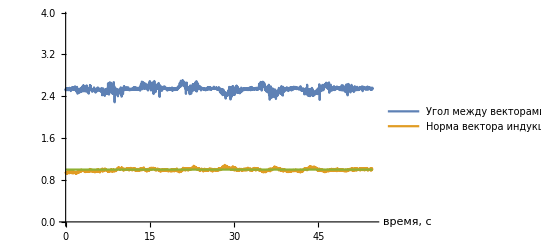

```mathematica
ugol=ListInterpolation[Ugol,{{0,Length[Kx]*h}}];
Plot[{ugol[t],ModM[t],1},{t,0,Length[Kx]*h},PlotRange->{0,5*Pi/4}, AxesLabel->{"время, с",""},PlotLegends->{"Угол между векторами гравитации и индукции","Норма вектора индукции"}]
```

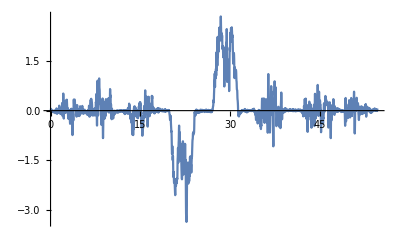

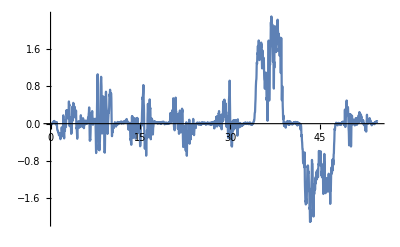

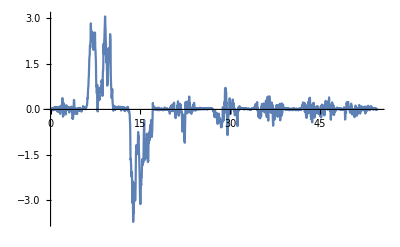

{{qw→InterpolatingFunction[{{0., 54.669}}, <>],qx→InterpolatingFunction[{{0., 54.669}}, <>],qy→InterpolatingFunction[{{0., 54.669}}, <>],qz→InterpolatingFunction[{{0., 54.669}}, <>]}}

```mathematica
fx=ListInterpolation[Kx,{{0,Length[Kx]*h}}];
fy=ListInterpolation[Ky,{{0,Length[Ky]*h}}];
fz=ListInterpolation[Kz,{{0,Length[Kz]*h}}];


Plot[fx[t],{t,0,Length[Kx]*h},PlotRange->All]
Plot[fy[t],{t,0,Length[Ky]*h},PlotRange->All]
Plot[fz[t],{t,0,Length[Kz]*h},PlotRange->All]
s=NDSolve[
{qw'[t]==-(fx[t]*qx[t]+fy[t]*qy[t]+fz[t]*qz[t])/2,
qx'[t]==(fx[t]*qw[t]-fy[t]*qz[t]+fz[t]*qy[t])/2,
qy'[t]==(fx[t]*qz[t]+fy[t]*qw[t]-fz[t]*qx[t])/2,
qz'[t]==(-fx[t]*qy[t]+fy[t]*qx[t]+fz[t]*qw[t])/2,
qx[0]==0,qy[0]==0,qz[0]==0,qw[0]==1},{qw,qx,qy,qz},
{t,0,Length[Kz]*h},MaxSteps->∞
]
```

```mathematica
J=Inverse[Transpose[{Normalize[Cross[Normalize[Cross[Aksel[[1]],Magn[[1]]]],Aksel[[1]]]],Normalize[Cross[Aksel[[1]],Magn[[1]]]], Normalize[Aksel[[1]]] }]];
NewMagn=Table[J.Magn[[i]], {i, 1, Length[M[[1]]]}];
NewAksel=Table[J.Aksel[[i]],{i,1,Length[M[[1]]]}];
```

```mathematica
NewMagn[[1]];
 NewAksel[[1]];
```

```mathematica
(*mg[i_]:=Normalize[Cross[NewAksel[[i]],NewMagn[[i]]]];  
msh[i_]:=Normalize[Cross[mg[i],NewAksel[[i]]]];
L=Table[Inverse[Transpose[{msh[i],mg[i],Normalize[NewAksel[[i]]]}]],{i,1,Length[M[[1]]]}];*)
```

Part::partd: Part specification Table⟦1⟧ is longer than depth of object.

```mathematica
(*file=File["C:\\1.TXT"]; str=OpenWrite[file]; *)
```

```mathematica
(*For[i=1, i≤Length[M[[1]]], i++,
T=mat[[i,0+1]]+mat[[i,5+1]]+mat[[i,10+1]]+1;
If [T>0, {S=0.5/Sqrt[T]; WW=0.25/S; XX=(mat[[i,9+1]]-mat[[i,6+1]])*S; YY=(mat[[i,2+1]]-mat[[i,8+1]])*S; ZZ=(mat[[i,4+1]]-mat[[i,1+1]])*S},
If[mat[[i,0+1]]≥mat[[i,5+1]] && mat[[i,0+1]]≥mat[[i,10+1]],{S=Sqrt[1.0+mat[[i,0+1]]-mat[[i,5+1]]-mat[[i,10+1]]]*2; XX=0.5/S; YY=(mat[[i,1+1]]+mat[[i,4+1]])/S; ZZ=(mat[[i,2+1]]+mat[[i,8+1]])/S; WW=(mat[[i,6+1]]+mat[[i,9+1]])/S}, 
If[mat[[i,5+1]]≥mat[[i,0+1]] && mat[[i,5+1]]≥mat[[i,10+1]],
{S=Sqrt[1.0+mat[[i,5+1]]-mat[[i,0+1]]-mat[[i,10+1]]]*2; XX=(mat[[i,1+1]]+mat[[i,4+1]])/S; YY=0.5/S; ZZ=(mat[[i,6+1]]+mat[[i,9+1]])/S; WW=(mat[[i,2+1]]+mat[[i,8+1]])/S}, {S=Sqrt[1.0+mat[[i,10+1]]-mat[[i,0+1]]-mat[[i,5+1]]]*2; XX=(mat[[i,2+1]]+mat[[i,8+1]])/S; YY=(mat[[i,6+1]]+mat[[i,9+1]])/S; ZZ=0.5/S; WW=(mat[[i,1+1]]+mat[[i,4+1]])/S} ]]

];
Write[str , Floor[WW,0.00001] ];
Write[str,Floor[XX,0.00001] ];
Write[str, Floor[YY,0.00001] ];
Write[str,Floor[ZZ,0.00001]  ];
]; *)
```

```mathematica
(*Close[str]; *)
```

```mathematica
Mt=Import["C:\\quat2.TXT","Table"]; M2=MatrixForm[Mt]; 
M2[[1,1]]
```

{1,0,0,0}

```mathematica
Length[M2[[1]]]
```

```mathematica
54669
```

```mathematica
54669
```

54669

```mathematica
KWW=Table[M2[[1,i,1]]/Sqrt[M2[[1,i,1]]*M2[[1,i,1]]+M2[[1,i,2]]*M2[[1,i,2]]+M2[[1,i,3]]*M2[[1,i,3]]+M2[[1,i,4]]*M2[[1,i,4]]],{i,1,Length[M2[[1]]],1}];
KxX=Table[M2[[1,i,2]]/Sqrt[M2[[1,i,1]]*M2[[1,i,1]]+M2[[1,i,2]]*M2[[1,i,2]]+M2[[1,i,3]]*M2[[1,i,3]]+M2[[1,i,4]]*M2[[1,i,4]]],{i,1,Length[M2[[1]]],1}];
KyY=Table[M2[[1,i,3]]/Sqrt[M2[[1,i,1]]*M2[[1,i,1]]+M2[[1,i,2]]*M2[[1,i,2]]+M2[[1,i,3]]*M2[[1,i,3]]+M2[[1,i,4]]*M2[[1,i,4]]],{i,1,Length[M2[[1]]],1}];
KzZ=Table[M2[[1,i,4]]/Sqrt[M2[[1,i,1]]*M2[[1,i,1]]+M2[[1,i,2]]*M2[[1,i,2]]+M2[[1,i,3]]*M2[[1,i,3]]+M2[[1,i,4]]*M2[[1,i,4]]],{i,1,Length[M2[[1]]],1}];
```

```mathematica
sinL[i_]:=Sqrt[1-KWW[[i]]*KWW[[i]]]*Sign[(L[[i,1,3]]-L[[i,3,1]]+L[[i,2,1]]-L[[i,1,2]]+L[[i,3,2]]-L[[i,2,3]])/(4*(KxX[[i]]+KyY[[i]]+KzZ[[i]])*KWW[[i]])];
```

```mathematica
Vect[i_]:={KxX[[i]],KyY[[i]],KzZ[[i]]};
OldVect[i_]:=Inverse[J].Vect[i];
```

Part::partw: Part 3 of {{0.0771201,0.077961,0.993969},{-0.996969,-0.00422004,0.0776839},{0.0102509,-0.996947,0.0773992}}.{{-0.101153,9.8376,-0.763754}}⟦1000⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

0.999998

```mathematica
X[t_]:=Evaluate[qy[t]/.s]* (-Evaluate[qy[t]/.s])-Evaluate[qz[t]/.s]* (Evaluate[qz[t]/.s])+Evaluate[qw[t]/.s]* (Evaluate[qw[t]/.s] )-Evaluate[qx[t]/.s]*(-Evaluate[qx[t]/.s]);Y[t_]:=-Evaluate[qx[t]/.s]* (-Evaluate[qy[t]/.s])+Evaluate[qw[t]/.s]*(Evaluate[qz[t]/.s])+Evaluate[qz[t]/.s]* (Evaluate[qw[t]/.s])-Evaluate[qy[t]/.s]* (-Evaluate[qx[t]/.s]);Z[t_]:=Evaluate[qw[t]/.s]* (-Evaluate[qy[t]/.s])+Evaluate[qx[t]/.s]* (Evaluate[qz[t]/.s])-Evaluate[qy[t]/.s]* (Evaluate[qw[t]/.s])-Evaluate[qz[t]/.s]* (-Evaluate[qx[t]/.s]);
X3[t_]:=-Evaluate[qx[t]/.s]* (-Evaluate[qy[t]/.s])-Evaluate[qw[t]/.s]*(Evaluate[qz[t]/.s])-Evaluate[qz[t]/.s]* (Evaluate[qw[t]/.s])-Evaluate[qy[t]/.s]* (-Evaluate[qx[t]/.s]);

Y3[t_]:=Evaluate[qy[t]/.s]* (Evaluate[qy[t]/.s])-Evaluate[qz[t]/.s]* (Evaluate[qz[t]/.s])+Evaluate[qw[t]/.s]* (Evaluate[qw[t]/.s] )+Evaluate[qx[t]/.s]*(-Evaluate[qx[t]/.s]);
Z3[t_]:=-Evaluate[qw[t]/.s]* (-Evaluate[qx[t]/.s])+Evaluate[qy[t]/.s]* (Evaluate[qz[t]/.s])+Evaluate[qx[t]/.s]* (Evaluate[qw[t]/.s])-Evaluate[qz[t]/.s]* (-Evaluate[qy[t]/.s]);


Ny=Import["C:\\Users\Sasha\Desktop\МГУ\Эксперименты 29.07.2019\Крен-Тангаж-Курс (эксперимент 1)\Controller3.TXT", "Table"]; 
NY=MatrixForm[Ny]; 
KZ0=Flatten[Table[NY[[1,i,4]],{i,1,Length[NY[[1]]],1}]];
KY0=Flatten[Table[NY[[1,i,3]],{i,1,Length[NY[[1]]],1}]];
KX0=Flatten[Table[NY[[1,i,2]],{i,1,Length[NY[[1]]],1}]];
KW0=Flatten[Table[NY[[1,i,1]],{i,1,Length[NY[[1]]],1}]];
b0=KW0[[1]]; 
b1=KX0[[1]];
b2=KY0[[1]];
b3=KZ0[[1]];
KW=Table[b0* KW0⟦i⟧+b1* KX0⟦i⟧+b2 *KY0⟦i⟧+b3 *KZ0⟦i⟧,{i,1,Length[NY[[1]]],1}];
KY=Table[-b1 *KW0⟦i⟧+b0* KX0⟦i⟧+b3 *KY0⟦i⟧-b2* KZ0⟦i⟧,{i,1,Length[NY[[1]]],1}];
KX=-Table[-b2 *KW0⟦i⟧-b3* KX0⟦i⟧+b0* KY0⟦i⟧+b1* KZ0⟦i⟧,{i,1,Length[NY[[1]]],1}];
KZ=Table[-b3 *KW0⟦i⟧+b2* KX0⟦i⟧-b1* KY0⟦i⟧+b0 *KZ0⟦i⟧,{i,1,Length[NY[[1]]],1}]; 

xW=ListInterpolation[KX,{{0,Length[Kz]*h}}]; 
yW=ListInterpolation[KY,{{0,Length[Kz]*h}}];
zW=ListInterpolation[KZ,{{0,Length[Kz]*h}}];
wW=ListInterpolation[KW,{{0,Length[Kz]*h}}];
X6[t_]:=yW[t]* (-yW[t])-zW[t]* (zW[t])+wW[t]* (wW[t] )-xW[t]*(-xW[t]);
Y6[t_]:=-xW[t]* (-yW[t])+wW[t]*(zW[t])+zW[t]* (wW[t])-yW[t]* (-xW[t]);  
Z6[t_]:=wW[t]* (-yW[t])+xW[t]* (zW[t])-yW[t]* (wW[t])-zW[t]* (-xW[t]);
```

```mathematica
KXX=Table[OldVect[i][[1]],{i,1,Length[M2[[1]]],1}];
KYY=Table[OldVect[i][[2]],{i,1,Length[M2[[1]]],1}];
KZZ=Table[OldVect[i][[3]],{i,1,Length[M2[[1]]],1}];
```

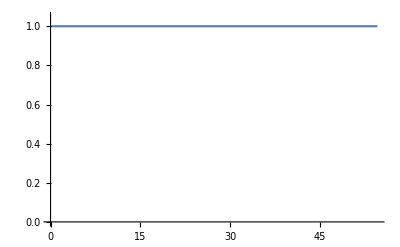

```mathematica
(*KWW=Table[b0* KW0⟦i⟧+b1* KX0⟦i⟧+b2 *KY0⟦i⟧+b3 *KZ0⟦i⟧,{i,1,Length[M[[1]]],1}];
KXX=Table[(-b1 *KW0⟦i⟧+b0* KX0⟦i⟧-b3 *KY0⟦i⟧+b2* KZ0⟦i⟧),{i,1,Length[M[[1]]],1}];
KYY=Table[(-b2 *KW0⟦i⟧+b3* KX0⟦i⟧+b0* KY0⟦i⟧-b1* KZ0⟦i⟧),{i,1,Length[M[[1]]],1}];
KZZ=Table[(-b3 *KW0⟦i⟧-b2* KX0⟦i⟧+b1* KY0⟦i⟧+b0 *KZ0⟦i⟧),{i,1,Length[M[[1]]],1}];*)
x2=ListInterpolation[KXX,{{0,Length[M2[[1]]]*h}}]; 
y2=ListInterpolation[KYY,{{0,Length[M2[[1]]]*h}}];
z2=ListInterpolation[KZZ,{{0,Length[M2[[1]]]*h}}];
w2=ListInterpolation[KWW,{{0,Length[M2[[1]]]*h}}];
X2[t_]:=y2[t]* (-y2[t])-z2[t]* (z2[t])+w2[t]* (w2[t] )-x2[t]*(-x2[t]);Y2[t_]:=-x2[t]* (-y2[t])+w2[t]*(z2[t])+z2[t]* (w2[t])-y2[t]* (-x2[t]);Z2[t_]:=w2[t]* (-y2[t])+x2[t]* (z2[t])-y2[t]* (w2[t])-z2[t]* (-x2[t]);  
norm4[t_]:=Norm[{X2[t],Y2[t],Z2[t]}];

Plot[(z2[t]*z2[t])+(x2[t]*x2[t])+(y2[t]*y2[t])+(w2[t]*w2[t]),{t,0,Length[Kz]*h},PlotRange->{{0, Length[Kz]*h} ,{0, 1.05}}]
```

```mathematica
wW[10.30]
```

0.799563

{{1,0,0},{0,1,0},{0,0,1}}

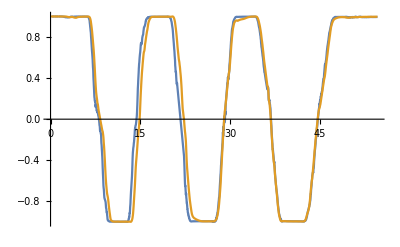

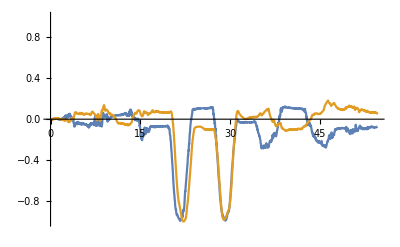

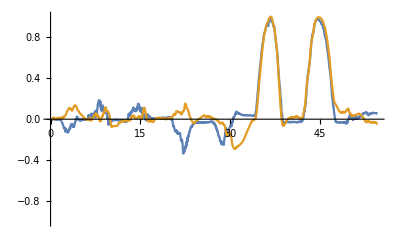

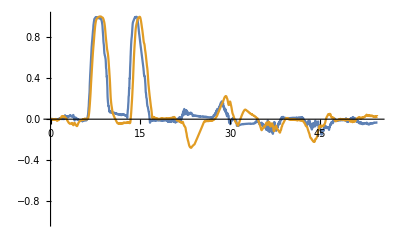

0.103771

-0.263897

```mathematica
Plot[{wW[t],w2[t]},{t,0,Length[Kz]*h},PlotRange->{-1,1}]
Plot[{xW[t],x2[t]},{t,0,Length[Kz]*h},PlotRange->{-1,1}]
Plot[{yW[t],y2[t]},{t,0,Length[Kz]*h},PlotRange->{-1,1}]
Plot[{zW[t],z2[t]},{t,0,Length[Kz]*h},PlotRange->{-1,1}]
w2[8]
```

```mathematica
norm1[t_]:=Sqrt[X[t]*X[t]+Y[t]*Y[t]+Z[t]*Z[t]];
norm2[t_]:=Sqrt[X3[t]*X3[t]+Y3[t]*Y3[t]+Z3[t]*Z3[t]];
norm3[t_]:=Norm[{X[t]*Z3[t]-Z[t]*Y3[t],Z[t]*X3[t]-X[t]*Z3[t],X[t]*Y3[t]-Y[t]*X3[t]}];
X4[t_]:=(X[t]*Z3[t]-Z[t]*Y3[t])/norm3[t];
Y4[t_]:=(Z[t]*X3[t]-X[t]*Z3[t])/norm3[t];
Z4[t_]:=(X[t]*Y3[t]-Y[t]*X3[t])/norm3[t];
```

```mathematica
Manipulate[
Graphics3D[{Parallelepiped[{0,0,0},{Flatten[{X[t]/norm1[t],Y[t]/norm1[t],Z[t]/norm1[t]}],Flatten[{X3[t]/norm2[t],Y3[t]/norm2[t],Z3[t]/norm2[t]}],Flatten[{X4[t],Y4[t],Z4[t]}]}],
Parallelepiped[{0,0,0},{Flatten[{X[t]/norm1[t],Y[t]/norm1[t],Z[t]/norm1[t]}],Flatten[{-X3[t]/norm2[t],-Y3[t]/norm2[t],-Z3[t]/norm2[t]}],Flatten[{X4[t],Y4[t],Z4[t]}]}],Parallelepiped[{0,0,0},{Flatten[{-X[t]/norm1[t],-Y[t]/norm1[t],-Z[t]/norm1[t]}],Flatten[{-X3[t]/norm2[t],-Y3[t]/norm2[t],-Z3[t]/norm2[t]}],Flatten[{X4[t],Y4[t],Z4[t]}]}],Parallelepiped[{0,0,0},{Flatten[{X[t]/norm1[t],Y[t]/norm1[t],Z[t]/norm1[t]}],Flatten[{X3[t]/norm2[t],Y3[t]/norm2[t],Z3[t]/norm2[t]}],Flatten[{-X4[t],-Y4[t],-Z4[t]}]}],Parallelepiped[{0,0,0},{Flatten[{-X[t]/norm1[t],-Y[t]/norm1[t],-Z[t]/norm1[t]}],Flatten[{X3[t]/norm2[t],Y3[t]/norm2[t],Z3[t]/norm2[t]}],Flatten[{-X4[t],-Y4[t],-Z4[t]}]}],Parallelepiped[{0,0,0},{Flatten[{X[t]/norm1[t],Y[t]/norm1[t],Z[t]/norm1[t]}],Flatten[{-X3[t]/norm2[t],-Y3[t]/norm2[t],-Z3[t]/norm2[t]}],Flatten[{-X4[t],-Y4[t],-Z4[t]}]}],Parallelepiped[{0,0,0},{Flatten[{-X[t]/norm1[t],-Y[t]/norm1[t],-Z[t]/norm1[t]}],Flatten[{-X3[t]/norm2[t],-Y3[t]/norm2[t],-Z3[t]/norm2[t]}],Flatten[{-X4[t],-Y4[t],-Z4[t]}]}],Parallelepiped[{0,0,0},{Flatten[{-X[t]/norm1[t],-Y[t]/norm1[t],-Z[t]/norm1[t]}],Flatten[{X3[t]/norm2[t],Y3[t]/norm2[t],Z3[t]/norm2[t]}],Flatten[{X4[t],Y4[t],Z4[t]}]}]},BoxRatios->{1,1,1}, ImageSize->800, PlotRange->{{-3, 3}, {-3, 3}, {-3, 3}}],
{t,0,Length[Kz]*h}]
```

```mathematica
((Sum[((xW[i*0.001]*x2[i*0.001])+(yW[i*0.001]*y2[i*0.001])+(zW[i*0.001]*z2[i*0.001])+(wW[i*0.001]*w2[i*0.001])),{i,0,Length[Kz]}])*100/(Length[Kz])+100)/2
```

97.9035

```mathematica
X05=Table[(Inverse[J].L[[i]].J.{1,0,0})[[1]],{i,1,Length[M[[1]]]}]; 
Y05=Table[(Inverse[J].L[[i]].J.{1,0,0})[[2]],{i,1,Length[M[[1]]]}];
Z05=Table[(Inverse[J].L[[i]].J.{1,0,0})[[3]],{i,1,Length[M[[1]]]}];
```

Part::partd: Part specification L⟦1⟧ is longer than depth of object.

Part::partd: Part specification L⟦2⟧ is longer than depth of object.

Part::partd: Part specification L⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification L⟦1⟧ is longer than depth of object.

Part::partd: Part specification L⟦2⟧ is longer than depth of object.

Part::partd: Part specification L⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification L⟦1⟧ is longer than depth of object.

Part::partd: Part specification L⟦2⟧ is longer than depth of object.

Part::partd: Part specification L⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
X5=ListInterpolation[X05,{{0,Length[M[[1]]]*h}}];  
Y5=ListInterpolation[Y05,{{0,Length[M[[1]]]*h}}];
Z5=ListInterpolation[Z05,{{0,Length[M[[1]]]*h}}];
```

```mathematica
Manipulate[
Graphics3D[Cylinder[{Normalize[{-X6[t],-Y6[t],-Z6[t]}],Normalize[{X6[t],Y6[t],Z6[t]}]},0.1],BoxRatios->{0.5,0.5,0.5}, ImageSize->500, PlotRange->{{-1.5, 1.5}, {-1.5, 1.5}, {-1.5, 1.5}}],
{t,0,Length[M[[1]]]*h}]
Manipulate[
Graphics3D[Cylinder[{{-X2[t],-Y2[t],-Z2[t]}/norm4[t],{X2[t],Y2[t],Z2[t]}/norm4[t]},0.1],BoxRatios->{0.5,0.5,0.5}, ImageSize->500, PlotRange->{{-1.5, 1.5}, {-1.5, 1.5}, {-1.5, 1.5}}],
{t,0,Length[M[[1]]]*h}]
```

Array::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of {-TagBox[InterpolatingFunction[{{« 2 »}}, {4, 7, 1, {« 1 »}, {« 1 »}, 0, 0, 0, 0, Automatic}, {{« 93237 »}}, {Developer`PackedArrayForm, {« 93238 »}, {« 186474 »}}, {Automatic}], False, Rule[Editable, False]][t_]^2 - TagBox[InterpolatingFunction[{{« 2 »}}, {4, 7, 1, {« 1 »}, {« 1 »}, 0, 0, 0, 0, Automatic}, « 1 », {Developer`PackedArrayForm, {« 93238 »}, {« 186474 »}}, {Automatic}], False, Rule[Editable, False]][t_]^2 + TagBox[InterpolatingFunction[{{0.`, 156.`}}, « 3 », {Automatic}], False, Rule[Editable, False]][t_]^2 + TagBox[InterpolatingFunction[{{0.`, 156.`}}, {4, 7, 1, {93237}, {4}, 0, 0, 0, 0, Automatic}, « 1 », {Developer`PackedArrayForm, {0, 2, « 47 », 98, « 93188 »}, {1.`, 0.`, 0.9999999997579252`, -0.000016950937437990686`, « 43 », -0.03831406933143553`, 0.9993601076027364`, -0.042645129088145925`, « 186424 »}}, {Automatic}], False, Rule[Editable, False]][t_]^2}, t.

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

```mathematica
A={{-2*YY,2*ZZ,-2*WW,2*XX},
{2*XX,2*WW,2*ZZ,2*YY},
{0,-4*XX,-4*YY,0},
{-2*nmagz[0]*YY,2*nmagz[0]*ZZ,-4*nmagx[0]*YY-2*nmagz[0]*WW,-4*nmagx[0]*ZZ+2*nmagz[0]*XX},
{-2*nmagx[0]*ZZ+2*nmagz[0]*XX,2*nmagx[0]*YY+2*nmagz[0]*WW,2*nmagx[0]*XX+2*nmagz[0]*ZZ,-2*nmagx[0]*WW+2*nmagz[0]*YY},
{2*nmagx[0]*YY,2*nmagx[0]*ZZ-4*nmagz[0]*XX,2*nmagx[0]*WW-4*nmagz[0]*YY,2*nmagx[0]*XX}};
w={2*(XX*ZZ-WW*YY)-naksx[i],
2*(WW*XX+YY*ZZ)-naksy[i],
2*(0.5-XX**2-YY**2)-naksz[i],
2*nmagx[0]*(0.5-YY**2-ZZ**2)+2*nmagz[0]*(XX*ZZ-WW*YY)-nmagx[i],
2*nmagx[0]*(XX*YY-WW*ZZ)+2*nmagz[0]*(WW*XX+YY*ZZ)-nmagy[i],
2*nmagx[0]*(WW*YY+XX*ZZ)+2*nmagz[0]*(0.5-XX**2-YY**2)-nmagz[i]};
Transpose[A].w
```

{-2 YY (2 (-WW YY+XX ZZ)-naksx[i])+2 XX (2 (WW XX+YY ZZ)-naksy[i])+(-2 ZZ nmagx[0]+2 XX nmagz[0]) (2 (XX YY-WW ZZ) nmagx[0]-nmagy[i]+2 (WW XX+YY ZZ) nmagz[0])+2 YY nmagx[0] (2 (WW YY+XX ZZ) nmagx[0]-nmagz[i]+2 nmagz[0] (0.5-XX**2-YY**2))-2 YY nmagz[0] (-nmagx[i]+2 (-WW YY+XX ZZ) nmagz[0]+2 nmagx[0] (0.5-YY**2-ZZ**2)),2 ZZ (2 (-WW YY+XX ZZ)-naksx[i])+2 WW (2 (WW XX+YY ZZ)-naksy[i])+(2 YY nmagx[0]+2 WW nmagz[0]) (2 (XX YY-WW ZZ) nmagx[0]-nmagy[i]+2 (WW XX+YY ZZ) nmagz[0])-4 XX (-naksz[i]+2 (0.5-XX**2-YY**2))+(2 ZZ nmagx[0]-4 XX nmagz[0]) (2 (WW YY+XX ZZ) nmagx[0]-nmagz[i]+2 nmagz[0] (0.5-XX**2-YY**2))+2 ZZ nmagz[0] (-nmagx[i]+2 (-WW YY+XX ZZ) nmagz[0]+2 nmagx[0] (0.5-YY**2-ZZ**2)),-2 WW (2 (-WW YY+XX ZZ)-naksx[i])+2 ZZ (2 (WW XX+YY ZZ)-naksy[i])+(2 XX nmagx[0]+2 ZZ nmagz[0]) (2 (XX YY-WW ZZ) nmagx[0]-nmagy[i]+2 (WW XX+YY ZZ) nmagz[0])-4 YY (-naksz[i]+2 (0.5-XX**2-YY**2))+(2 WW nmagx[0]-4 YY nmagz[0]) (2 (WW YY+XX ZZ) nmagx[0]-nmagz[i]+2 nmagz[0] (0.5-XX**2-YY**2))+(-4 YY nmagx[0]-2 WW nmagz[0]) (-nmagx[i]+2 (-WW YY+XX ZZ) nmagz[0]+2 nmagx[0] (0.5-YY**2-ZZ**2)),2 XX (2 (-WW YY+XX ZZ)-naksx[i])+2 YY (2 (WW XX+YY ZZ)-naksy[i])+(-2 WW nmagx[0]+2 YY nmagz[0]) (2 (XX YY-WW ZZ) nmagx[0]-nmagy[i]+2 (WW XX+YY ZZ) nmagz[0])+2 XX nmagx[0] (2 (WW YY+XX ZZ) nmagx[0]-nmagz[i]+2 nmagz[0] (0.5-XX**2-YY**2))+(-4 ZZ nmagx[0]+2 XX nmagz[0]) (-nmagx[i]+2 (-WW YY+XX ZZ) nmagz[0]+2 nmagx[0] (0.5-YY**2-ZZ**2))}